# Optimización de Rutas en Vehiculos Automotores Responsable del Proyecto: M. en C. Fidel González Gutiérrez

# Alumnas de Bachillerato Avanzado: Sofia Arteaga, Amairani Rayas, Andrea Tapia, Yunnuen Ochoa

## Modelado de Zona Urbana a través de un Grafo

Aristas Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges={1->2, 1->3,1->4,2->3,2->5,2->6,3->4,3->6,3->7,4->7,5->6,5->8,6->7,6->8,7->8}
eWeigth={16,10,5,2,6,4,4,12,10,15,8,7,3,16,5}
coord={{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}}
```

{1->2,1->3,1->4,2->3,2->5,2->6,3->4,3->6,3->7,4->7,5->6,5->8,6->7,6->8,7->8}

{16,10,5,2,6,4,4,12,10,15,8,7,3,16,5}

{{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}}

Aristas No Dirigidas, Pesos de Aristas y Coordenadasde Vértices

```mathematica
nEdges={1<->2, 1<->3,1<->4,2<->3,2<->5,2<->6,3<->4,3<->6,3<->7,4<->7,5<->6,5<->8,6<->7,6<->8,7<->8}
eWeigth={16,10,5,2,6,4,4,12,10,15,8,7,3,16,5}
coord={{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}}
```

{1<->2,1<->3,1<->4,2<->3,2<->5,2<->6,3<->4,3<->6,3<->7,4<->7,5<->6,5<->8,6<->7,6<->8,7<->8}

{16,10,5,2,6,4,4,12,10,15,8,7,3,16,5}

{{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}}

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges]
Length[eWeigth]
```

15

15

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]]
```

{1<->2→16,1<->3→10,1<->4→5,2<->3→2,2<->5→6,2<->6→4,3<->4→4,3<->6→12,3<->7→10,4<->7→15,5<->6→8,5<->8→7,6<->7→3,6<->8→16,7<->8→5}

Construcción del Gráfo a partir de las Aristas, Pesos y Coordenadas

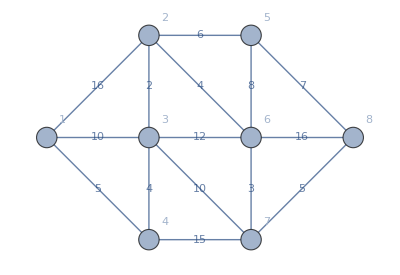

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges]
```

## Optimización de Rutas Vehiculares

Algoritmo para el Cálculo de la Ruta Corta Grafos No Dirigidos

```mathematica
rutaCortaN[grafo_,origen_,destino_]:=Module[{g,g1,path,peso},g=grafo;
path=FindShortestPath[g,origen,destino];
g1=HighlightGraph[g,PathGraph[path]];
peso=GraphDistance[g,origen,destino,Method->"Dijkstra"];
{g1,path,peso}
]
```

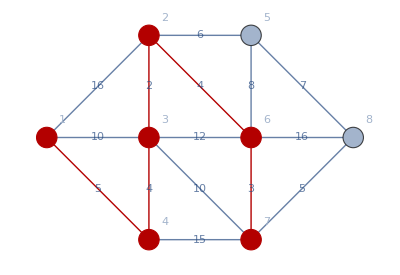
{-Graphics-,{1,4,3,2,6,7},18.}

```mathematica
rutaCortaN[g,1,7]
```

Algoritmo para el Cálculo de la Ruta Corta Grafos  Dirigidos

```mathematica
rutaCortaD[grafo_,origen_,destino_]:=Module[{g,g1,path,path1,peso},g=grafo;
path=FindShortestPath[g,origen,destino];
path1=Map[path_⟦#⟧->path_⟦#+1⟧&,Range[Length[path]-1]];
g1=HighlightGraph[g,PathGraph[path1]];
peso=GraphDistance[g,origen,destino,Method->"Dijkstra"];
{g1,path,peso}
]
```

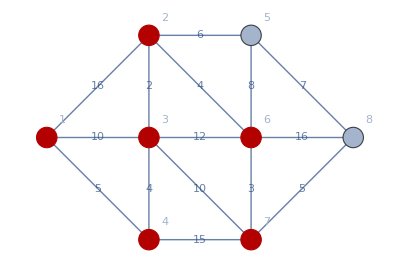
{-Graphics-,{1,4,3,2,6,7},18.}

```mathematica
rutaCortaD[g,1,7]
```

Simulación Interactiva para el Cálculo de la Ruta Corta en un Gráfo No Dirigido
qwddqwd

```mathematica
Manipulate[rutaCortaN[g,Origen,Destino],{{Origen,1},Range[8],ControlType->PopupMenu},{{Destino,2},Range[8],ControlType->PopupMenu}]
```

Simulación Interactiva para el Cálculo de la Ruta Corta en un Gráfo Dirigido

```mathematica
Manipulate[rutaCortaD[g,Origen,Destino],{{Origen,1},Range[8],ControlType->PopupMenu},{{Destino,8},Range[8],ControlType->PopupMenu}]
```

## Algorimo para la simplificacion del MLC

```mathematica
GetLeftVertices [S_]:= VertexList[S]

ListOfLefts[S_, V_] := Module[{lefts,g, vertices}, 
g = S;
vertices=V;
For[ x =1, x<Length[g], x++
If[VertexDegree[g,V[x]] ==1,
Append[lefts, V[x]]
,
](*FIN DEL IF*)
](*FIN DEL FOR*)
{lefts}
]


ReduceMLC[S_, G_]:= Module[{aristaEliminada, leaftVertices, R,verticeAux },
aristaEliminada = false;
While[aristaEliminada == false,
leaftVertices = VertexList[S];
leaftVertices = Sort[leaftVertices];
For[x=0, x<Length[leaftVertices],x++,
verticeAux = leftVertices[[x]];
R = VertexDelete[S,verticeAux];
R = EdgeDelete[R,incidente[verticeAux]];
If[EsInstanciaMLC[R],
aristaElminada = true;
S = R;
Break[]
,
](*FIN DEL IF*)
](*FIN DEL CICLO FOR*)
](*FIN DEL CICLO WHILE*)
{S}
](*FIN DE LA FUNCION*)


ListOfVertex
```

```mathematica
GetLeftVertices[g];
VertexList[g];
listaArista = Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
listaArista = SortBy[listaArista, Last ];
g
listaArista = Reverse[listaArista]
VertexDegree[g,6]
arit = true
```

-Graphics-

{6<->8→16,1<->2→16,4<->7→15,3<->6→12,3<->7→10,1<->3→10,5<->6→8,5<->8→7,2<->5→6,7<->8→5,1<->4→5,3<->4→4,2<->6→4,6<->7→3,2<->3→2}

5

true